This program processes the data from the coincidence simulations. Histograms for each detector are shown, as well as a listplot of concident events for energies above a certain cutoff.

```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["coinc1.txt","Data"];
data2 = Import["coinc2.txt","Data"];
roseE= Import["roseE.txt","Data"];
roseM= Import["roseM.txt","Data"];
stieblingE=Import["stieblingE.txt","Data"];
stieblingM=Import["stieblingM.txt","Data"];
```

```mathematica
data = Flatten[data];
data2 = Flatten[data2];
roseE=Flatten[roseE];
roseM=Flatten[roseM];
stieblingE=Flatten[stieblingE];
stieblingM=Flatten[stieblingM];


weights={};
For[i=1,i≤Length[data],++i,
AppendTo[weights, roseE[[i]] + roseM[[i]]];
]
weights2=weights;

detector1={};
detector2={};
weights1new={};
weights2new={};

For[i=1,i≤Length[data],++i,
If[data[[i]]>0.,AppendTo[detector1,data[[i]]];
AppendTo[weights1new,weights[[i]]];]
]
For[i=1,i≤Length[data2],++i,
If[data2[[i]]>0.,AppendTo[detector2,data2[[i]]];
AppendTo[weights2new,weights2[[i]]];]
]


dataW=WeightedData[detector1,weights1new];
data2W=WeightedData[detector2,weights2new];
hist=HistogramDistribution[dataW, {.2}];
hist2=HistogramDistribution[data2W, {.2}];
```

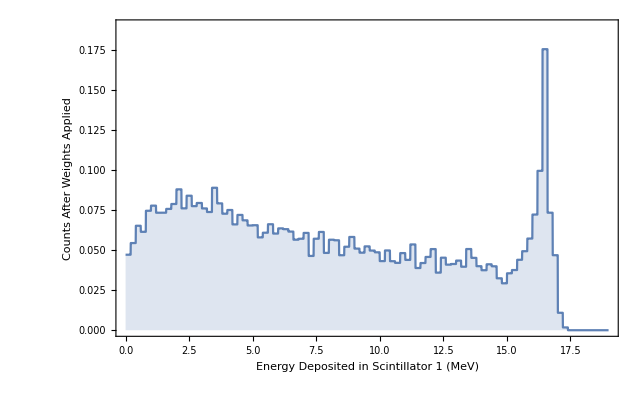

```mathematica
Plot[PDF[hist,x],{x,0,19},Filling->Axis,Exclusions->None,PlotRange->{0,.19},RotateLabel->True,FrameLabel->{Style["Energy Deposited in Scintillator 1 (MeV)",20,Bold,Blue],Style["Counts After Weights Applied",20,Bold,Blue]},
LabelStyle->Directive[Blue,Bold],Frame->True]
```

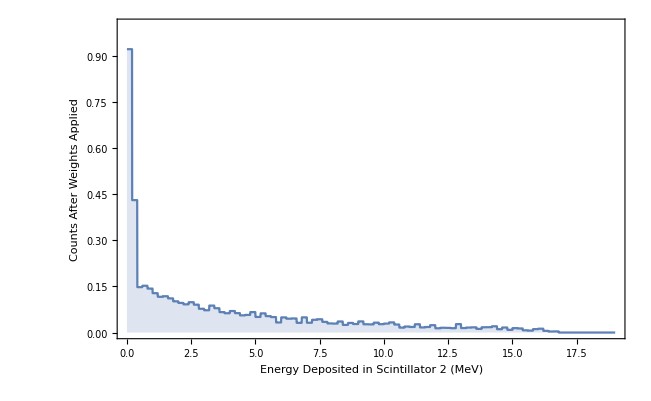

```mathematica
Plot[PDF[hist2,x],{x,0,19},Filling->Axis,Exclusions->None,PlotRange->{0,1},RotateLabel->True,FrameLabel->{Style["Energy Deposited in Scintillator 2 (MeV)",20,Bold,Blue],Style["Counts After Weights Applied",20,Bold,Blue]},
LabelStyle->Directive[Blue,Bold],Frame->True]
```

```mathematica
sampleDetector1=RandomVariate[hist,100000];
sampleDetector2=RandomVariate[hist2,100000];
count =0;
```

```mathematica
coincidentEvents={};
For[i=1,i≤Length[sampleDetector1],++i,
If[sampleDetector1[[i]]>2&&sampleDetector2[[i]]>2&& ((sampleDetector1[[i]]+sampleDetector2[[i]])>15) &&((sampleDetector1[[i]]+sampleDetector2[[i]])<=17.885) , AppendTo[coincidentEvents,{sampleDetector1[[i]],sampleDetector2[[i]]}]];
If[sampleDetector1[[i]]>2 && ((sampleDetector1[[i]]+sampleDetector2[[i]])<=17.885),count=count+1]
]
```

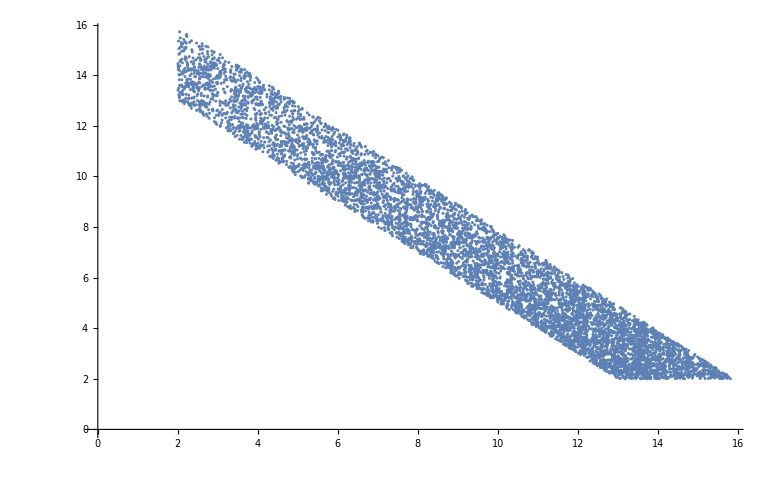

```mathematica
ListPlot[coincidentEvents]
```